```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];
```

## Parámetros

```mathematica
(*HNL DECAYS TOO MESONS/LEPTONS*)(*ESTE SCRIPT GENERA LOS ARCHIVOS PCONFIG QUE UTILIZA PYTHIA8.*)(*NOTAR QUE SIEMPRE TOMA COMO ARGUMENTO LA MASA DEL HNL*)e=0.5109989461*10^-3;
mu=105.6583745*10^-3;
tau=1.77686;
leptons={e,mu,tau};
tfactor=1.5193*10^24(*Para pasar de s a GeV^-1*);mmc=3*10^11(*para pasar de s a mm/c*);
ckm=({{0.9742,0.2243,0.0365},{0.218,0.997,0.0422},{0.0081,0.0394,1.019}});
gf=1.166378*10^-5;
xw=0.2223;
gll=-(1/2)+xw;
glr=xw;

(*charged pseudoscalar*)
(* 1.tau 2.m 3.f 4.CKM 5.id*)
d431={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],431};
d431bar={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],-431};
d411={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],411};
d411bar={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],-411};
k321={1.238*10^-8*tfactor,493.677*10^-3,155.6*10^-3,ckm[[1,2]],321};
pi211={2.6*10^-8*tfactor,139.57061*10^-3,130.2*10^-3,ckm[[1,1]],211};

d421={410.1*10^-15*tfactor,1.86483,Null,Null,421};
k311={Null,0.497611,Null,Null,311};

(*Charged vector*)
k323={Null,895.55*10^-3,0.1827,ckm[[1,2]]}(*K*(892)*);
rho770c={Null,775.26*10^-3,0.162,ckm[[1,1]]};

(*neutral pseudoscalar*)
pi111={Null,134.977*10^-3,130.2*10^-3,Null};
eta221={Null,547.862*10^-3,81.7*10^-3,Null}(*eta*);eta331={Null,957.78*10^-3,-94.7*10^-3,Null}(*eta prime*);
(*Neutral vector*)
rho770n={Null,775.26*10^-3,0.162,1-2xw};
omega782={Null,782.65*10^-3,0.153,4/3 xw};
phi1020={Null,1.019461,0.234,4/3 xw-1};

datae=Import[NotebookDirectory[]<>"/mainconfig/mixe.dat"];
datamu=Join[Table[{i,1},{i,0.01,0.1,0.01}],Import[NotebookDirectory[]<>"/mainconfig/mixmu.dat"]];
datatau=Import[NotebookDirectory[]<>"/mainconfig/mixtau.dat"];
fmixe=Interpolation[datae,InterpolationOrder->1];
fmixmu=Interpolation[datamu,InterpolationOrder->1];
fmixtau=Interpolation[datatau,InterpolationOrder->1];
```

# 2 body decays

```mathematica
(***************MESON DECAY*******************)
(*meson decay BRs function*)
width2body[meson_,l_,n_,u_]:=Re[(gf^2*meson[[3]]^2*meson[[2]]*n^2)/(8*Pi)*meson[[4]]^2*u^2*(1-n^2/meson[[2]]^2+2l^2/meson[[2]]^2+l^2/n^2(1-l^2/meson[[2]]^2))*Sqrt[(1+n^2/meson[[2]]^2-l^2/meson[[2]]^2)^2-4*n^2/meson[[2]]^2]*UnitStep[meson[[2]]-l]];
newwidth[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[1/meson[[1]]+width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
newwidth2hnl[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
(*BRs solo a HNL,normalizados a 1*)
meson2bodybr[meson_,l_,n_,u_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,l,n,u]/newwidth2hnl[meson,n,mixe,mixmu,mixtau]];
```

```mathematica
bre[meson_,n_]:=width2body[meson,e,n,√fmixe[n]]/newwidth[meson,n,√fmixe[n],√fmixmu[n],√fmixtau[n]];
brmu[meson_,n_]:=width2body[meson,mu,n,√fmixmu[n]]/newwidth[meson,n,√fmixe[n],√fmixmu[n],√fmixtau[n]];
brtoy[meson_,l_,n_]:=width2body[meson,l,n,1]/newwidth[meson,n,1,1,1];
```

```mathematica
magnificationlegends=1;
latexe=MaTeX["D_s^+\\rightarrow e^+N",Magnification->magnificationlegends,ContentPadding->False];
latexmu=MaTeX["D_s^+\\rightarrow \\mu^+N",Magnification->magnificationlegends,ContentPadding->False];
latextau=MaTeX["D_s^+\\rightarrow \\tau^+\\nu_\\tau",Magnification->magnificationlegends,ContentPadding->False];
ylabel=MaTeX["\\text{BR}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["m_\\text{HNL}",Magnification->magnificationlegends,ContentPadding->False];
legends={latexe,latexmu,latextau};
```

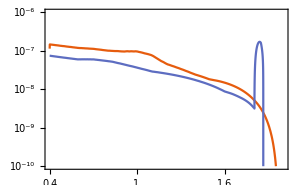

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0.4,2}, {1*10^-10,1*10^-6}};
imagesize={300,Automatic};
plotpoints=5000;
ticksx=Table[i,{i,0.4,2.,0.2}];
ticksy={{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"}};
frameticks={{ticksy,None},{ticksx,Automatic}};
colours={pltcolors[[1]],pltcolors[[2]],pltcolors[[3]]};
framelabel={xlabel,ylabel};
plotlegends=Placed[LineLegend[Join[Table[{colours[[i]]},{i,1,Length@colours-1}],{Null}],Table[legends[[i]],{i,1,Length@legends-1}],Spacings->0.1,LegendLayout->{"Column",1},LegendMarkerSize->12],{0.675,0.825}];
bg=Plot[{Null,Null},{n,0.5,2},PlotTheme->plottheme,ScalingFunctions->scalingfunctions,PlotPoints->plotpoints,ImageSize->imagesize,PlotRange->plotrange,FrameTicks->frameticks,PlotStyle->colours,PlotLegends->plotlegends,FrameLabel->framelabel];
plote=Plot[bre[d431,n],{n,0.4,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->colours[[1]]];
plotmu=Plot[brmu[d431,n],{n,0.4,1.8},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->colours[[2]]];
plotmuaux=Plot[brmu[d431,n],{n,1.8,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->5000,PlotStyle->colours[[2]]];
plotexp=Show[bg,plote,plotmu,plotmuaux]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/br431.pdf",plotexp];
```

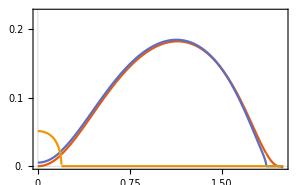

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Linear"};
plotrange = {{0,2}, {0,0.225}};
imagesize={300,Automatic};
plotpoints=5000;
ticksx=Automatic;
ticksy=Table[{i,ToString[i]},{i,0,0.2,0.05}];
frameticks={{ticksy,None},{ticksx,Automatic}};
colours={pltcolors[[1]],pltcolors[[2]],pltcolors[[3]]};
framelabel={xlabel,ylabel};
plotlegends=Placed[LineLegend[Join[Table[{colours[[i]]},{i,1,Length@colours}],{Null}],Table[legends[[i]],{i,1,Length@legends}],Spacings->0.1,LegendLayout->{"Column",1},LegendMarkerSize->12],{0.2,0.8}];
bg=Plot[{Null,Null},{n,0,2},PlotTheme->plottheme,ScalingFunctions->scalingfunctions,PlotPoints->plotpoints,ImageSize->imagesize,PlotRange->plotrange,FrameTicks->frameticks,PlotStyle->colours,PlotLegends->plotlegends,FrameLabel->framelabel];
plote=Plot[brtoy[d431,e,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[1]]];
plotmu=Plot[brtoy[d431,mu,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[2]]];
plottau=Plot[brtoy[d431,tau,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[3]]];
plotexp=Show[bg,plote,plotmu,plottau]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/brtoy431.pdf",plotexp];
```

# 3 body Bondarenko (pp 26, 38)

Existe una diferencia con Graverini de ~50%. Pero esto puede deberse a los form factors.

```mathematica
z[meson1_,meson2_,q2_]:=Module[{tp,t0},
tp=(meson1[[2]]+meson2[[2]])^2;
t0=(meson1[[2]]+meson2[[2]])(√meson1[[2]]-√meson2[[2]])^2;
(√(tp-q2)-√(tp-t0))/(√(tp-q2)+√(tp-t0))];
```

```mathematica
lambda[a_,b_,c_]:=a^2+b^2+c^2-2a*b-2a*c-2b*c;
```

```mathematica
fp[meson1_,meson2_,q2_]:=Module[
{f0, c, P},
If[(meson1[[5]]==411||meson1[[5]]==421)&& (meson2[[5]]==321||meson2[[5]]==311),
f0=0.7647; c=0.066; P=0.224];
If[(meson1[[5]]==411||meson1[[5]]==421)&& meson2[[5]]==211,
f0=0.6117; c=1.985; P=0.1314];
1/(1-P*q2)*(f0-c(z[meson1,meson2,q2]-z[meson1,meson2,0])(1+(z[meson1,meson2,q2]+z[meson1,meson2,0])/2))
];
```

```mathematica
f0[meson1_,meson2_,q2_]:=Module[
{f0, c, P},
If[(meson1[[5]]==411||meson1[[5]]==421)&& (meson2[[5]]==321||meson2[[5]]==311),
f0=0.7647; c=2.084; P=0];
If[(meson1[[5]]==411||meson1[[5]]==421)&& meson2[[5]]==211,
f0=0.6117; c=1.188; P=0.0342];
1/(1-P*q2)*(f0-c(z[meson1,meson2,q2]-z[meson1,meson2,0])(1+(z[meson1,meson2,q2]+z[meson1,meson2,0])/2))
];
```

```mathematica
Lambda[meson1_,meson2_,l_,n_,xi_]:=√lambda[1,(meson2[[2]]/meson1[[2]])^2,xi]*√lambda[xi,(n/meson1[[2]])^2,(l/meson1[[2]])^2];
gminus[meson1_,meson2_,l_,n_,xi_]:=xi*((n/meson1[[2]])^2+(l/meson1[[2]])^2)-((n/meson1[[2]])^2-(l/meson1[[2]])^2)^2;
```

```mathematica
ip1[meson1_,meson2_,l_,n_]:=
NIntegrate[1/(3 xi^3)*fp[meson1,meson2,xi*meson1[[2]]^2]^2*Lambda[meson1,meson2,l,n,xi]^3,{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}];
```

```mathematica
ip2[meson1_,meson2_,l_,n_]:=
NIntegrate[1/(2 xi^3)*fp[meson1,meson2,xi*meson1[[2]]^2]^2*Lambda[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]*lambda[1,(meson2[[2]]/meson1[[2]])^2,xi],{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}];
```

```mathematica
ip3[meson1_,meson2_,l_,n_]:=
NIntegrate[1/(2 xi^3)*f0[meson1,meson2,meson1[[2]]^2*xi]^2*Lambda[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]*(1-(meson2[[2]]/meson1[[2]])^2)^2,{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}];
```

```mathematica
sigma3body[meson1_,meson2_,l_,n_,u_]:=Module[{ck},
If[meson2[[5]]==211,ck=1/(√2),ck=1];
(gf^2 meson1[[2]]^5)/(64 Pi^3)*ck^2*ckm[[2,2]]^2 u^2(ip1[meson1,meson2,l,n]+ip2[meson1,meson2,l,n]+ip3[meson1,meson2,l,n])];
```

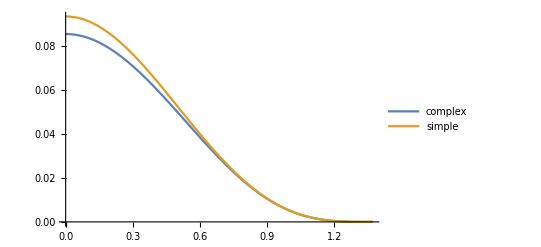

```mathematica
Plot[{sigma3body[d411,k311,e,n,1]/(d411[[1]]^-1+sigma3body[d411,k311,e,n,1]),d411[[1]]*sigma3body[d411,k311,e,n,1]},{n,0,d411[[2]]-k311[[2]]-e},PlotLegends->{"complex","simple"}]
```

# 3 Body decays GRAVERINI (incompleto)

```mathematica
md0=1.86483;
mdscalar=2.318;
mdvector=2.01026;
mk=.493677;
me=e;
fpd[x_]:=0.747/(1-x/mdvector^2);
f0d[x_]:=0.747/(1-x/mdscalar^2);
fmd[x_]:=(md0^2-mk^2)/x(f0d[x]-fpd[x]);
factor=(410.1*10^-15*tfactor)(1)^2(ckm[[2,2]]^2 gf^2)/(64 Pi^3 md0^2);
d03[h1_,h2_,l_,n_]:=factor*
NIntegrate[
fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)
+2fpd[x]*fmd[x](n^2(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
+l^2(4y*h1+l^2-n^2-x))
+fpd[x]^2((4y*h1+l^2-n^2-x)(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
-(2 h1^2+2 h2^2-x)(x-n^2-l^2))
,{x,(l+n)^2,(h1-h2)^2},{y,n,(h1^2+n^2-(l+h2)^2)/(2h1)},Method->"GlobalAdaptive"];
```

```mathematica
d03toy[h1_,h2_,l_,n_]:=factor*
NIntegrate[
fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)
+2fpd[x]*fmd[x](n^2(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
+l^2(4y*h1+l^2-n^2-x))
+fpd[x]^2((4y*h1+l^2-n^2-x)(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
-(2 h1^2+2 h2^2-x)(x-n^2-l^2))
,{x,(l+n)^2,(h1-h2)^2},{y,n,2n},Method->"GlobalAdaptive"];
```

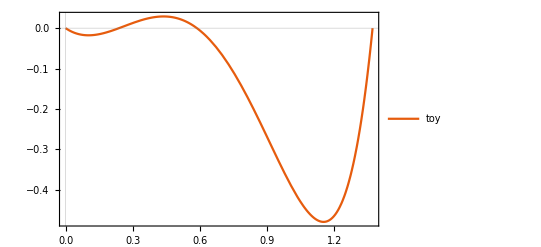

```mathematica
Plot[{d03toy[md0,mk,e,n]},{n,0,md0-mk-e},PlotTheme->"Scientific",PlotRange->All,PlotLegends->{"toy","old"}]
```

```mathematica
d03toy[md0,mk,e,0.3]
```

0.23322

```mathematica
NIntegrate
```

```mathematica
n=0.05;
l=e;
h=mk;
Re[Integrate[Integrate[fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)+2fpd[x]fmd[x](n^2(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)+l^2(4y*md0+l^2-n^2-x))+fpd[x]^2((4y*md0+l^2-n^2-x)(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)-(2 md0^2+2 h^2-x)(x-n^2-l^2)),{x,(l+n)^2,(md0-h)^2}],{y,n,(md0^2+n^2-(l+h)^2)/(2md0)}]]
```

-1.10123

```mathematica
d03[h_,l_,n_]:=NIntegrate[fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)+2fpd[x]fmd[x](n^2(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)+l^2(4y*md0+l^2-n^2-x))*fpd[x]^2((4y*mk+l^2-n^2-x)(2 mk^2-2 mpi^2-4y*mk-l^2+n^2+x)-(2 mk^2+2 mpi^2-x)(x-n^2-l^2)),{x,(l+n)^2,(md0-h)^2},{y,n,(md0^2+n^2-(l+h)^2)/(2md0)}]
```

```mathematica
Length
```

```mathematica
ds2[l_,n_]:=(1-n^2/mds^2+2 l^2/mds^2+l^2/n^2(1-l^2/mds^2))√((1+n^2/mds^2-l^2/mds^2)^2-4*n^2/mds^2);
```

```mathematica
ds2[me,1]*356*10^-12
```

1.95897×10^-10